# WordGraph

Create a word graph

## Definition

```mathematica
WordGraph[dictionary_,start_,nestlevel_,distancefunction_:HammingDistance,threshold_:1]:=NestGraph[(word↦Select[distancefunction[word,#]==threshold&][dictionary]),start,nestlevel,VertexLabels->Automatic]
```

## Documentation

### Usage

WordGraph[dictionary, start, nestlevel]

creates a word graph by nesting nestlevel times to find words that have a Hamming distance of 1 from the string or word start based on the data in dictionary.

WordGraph[dictionary,start,nestlevel,distancefunction,threshold]

creates a word graph by nesting nestlevel times to find words that have a distance of threshold based on the string distance function distancefunction from the string or word start based on the data in dictionary.

### Details & Options

String distance functions include HammingDistance and DamerauLevenshteinDistance and EditDistance

## Examples

### Basic Examples

Create a word graph starting from tears with the WordList by going 5 levels deep based:

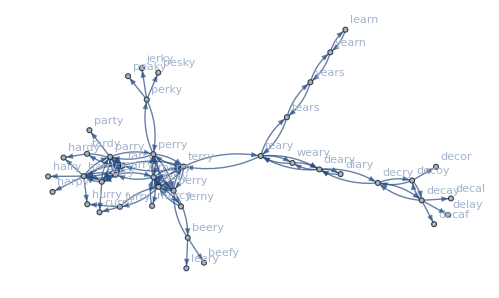

```mathematica
WordGraph[WordList[],"tears",5]
```

Create a word graph starting from tears with the WordList by going 2 levels deep based on words that differ by 2 using DamerauLevenshteinDistance:

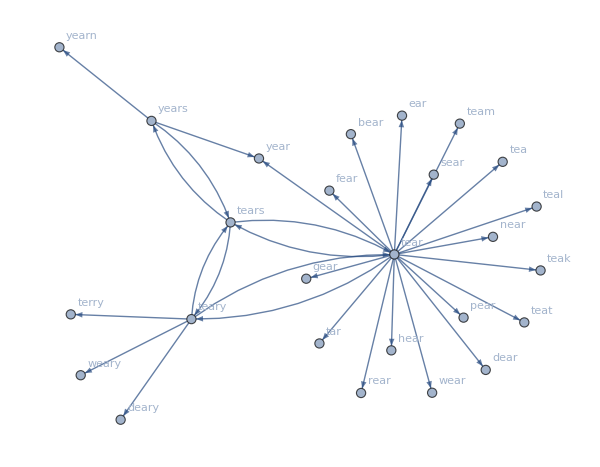

```mathematica
WordGraph[WordList[],"tears",2,DamerauLevenshteinDistance,1]
```

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

### Applications

### Properties and Relations

### Possible Issues

### Neat Examples

Compare the sizes of graphs based on different distance rules:

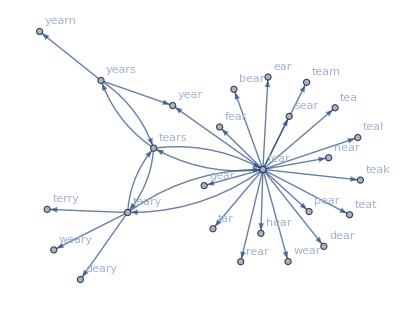
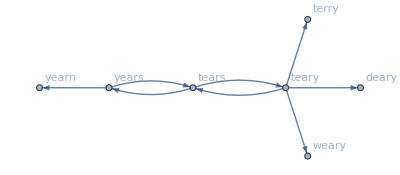
<|EditDistance→-Graphics-,HammingDistance→-Graphics-,DamerauLevenshteinDistance→-Graphics-|>

```mathematica
AssociationMap[distancefunction↦WordGraph[WordList[],"tears",2,distancefunction,1],{EditDistance,HammingDistance,DamerauLevenshteinDistance}]
```

## Source & Additional Information

### Contributed By

Peter Burbery

### Keywords

words

dictionaries

graph theory

nesting

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

NestGraph

HammingDistance

EditDistance

DamerauLevenshteinDistance

### Related Resource Objects

WordCloudFromNames

WordWeave

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.